## Setup

```mathematica
Get["FunKit`"]
```

Mathematica package TensorBases loaded

Authors: Andreas Geißel, Franz Richard Sattler

Version: 1.0

Year: 2025

For a list of available bases, call TBInfo[]. For further information on a particular basis, call TBInfo["BasisName"].

This package provides the methods TBGetBasisElement, TBGetInnerProduct, TBGetMetric, TBGetInverseMetric, TBGetProjector for every tensor basis available.

For closer explanations, please call their usage messages, e.g. TBGetProjector::usage.

Other useful tools include TBBasisTransformation, TBVertexTransformation, TBGetIdentityMatrix, TBGetBasisSize, TBGetIndexSet, TBMakePropagator.

To build or manipulate bases, please call TBInfo["BaseBuilder"].

To show information on the used notation, call TBInfo["Notation"].

FormTracer package already loaded.

Clearing all extra variables for compatibility!

To see all (user-defined and package-defined) FormTracer definitions, call TBInfo["FormTracer"].

Furthermore, TensorBases extends FormTracer. To see all extensions, call TBInfo["Extensions"]

To see all momentum transformations that can be performed by TensorBases, call TBInfo["Momenta"].

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 0.4.0
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

The following defines the scalar field theory and the truncation used. Here, the symmetric phase is assumed by setting Field->{} in the truncation. 
Warning: Setting Field->{ϕ} will give the results for the broken phase, but this will also greatly increase the number of terms in the four- and six-point functions, which may take a long time to compute.

```mathematica
fields= <|
"Commuting"-> {ϕ[p]},
"Grassmann"->{}
|>;
truncation=<|
GammaN->{{ϕ,ϕ},{ϕ,ϕ,ϕ,ϕ}},
Propagator->{{ϕ,ϕ}},
G->{{ϕ,ϕ}},
Rdot->{{ϕ,ϕ}},
S->{{ϕ,ϕ},{ϕ,ϕ,ϕ,ϕ}},
Field->{}
|>;
setup=<|
"FieldSpace"->fields,
"Truncation"->truncation
|>;
FSetGlobalSetup[setup];
```

If you would like to see what FunKit does underneath, you can set the debug level to values greater than 0. The numbers correspond to the following level of detail:
0: no info
1: basic information what is happening
2: in-depth what steps are being processed
3: the guts of the program
4: nested guts of the program
5: all details
6: information only needed for debugging

```mathematica
FSetDebugLevel[0];
```

## DSE

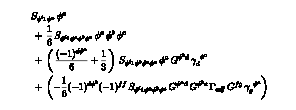

```mathematica
DSE=FMakeDSE[ϕ[i1]]//FPrint;
```


-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
DSE2P=FTakeDerivatives[DSE,{ϕ[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

```mathematica
DSE4P=FTakeDerivatives[DSE,{ϕ[i2],ϕ[i3],ϕ[i4]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
DSE6P=FTakeDerivatives[DSE,{ϕ[i2],ϕ[i3],ϕ[i4],ϕ[i5],ϕ[i6]}]//FTruncate//FPlot//FRoute//FPrint;
```

## fRG

```mathematica
fRG2P=FTakeDerivatives[WetterichEquation,{ϕ[i1],ϕ[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-

-Graphics-

```mathematica
fRG4P=FTakeDerivatives[WetterichEquation,{ϕ[i1],ϕ[i2],ϕ[i3],ϕ[i4]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-

-Graphics-

```mathematica
fRG6P=FTakeDerivatives[WetterichEquation,{ϕ[i1],ϕ[i2],ϕ[i3],ϕ[i4],ϕ[i5],ϕ[i6]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-

-Graphics-

## 3PI

```mathematica
FAddCorrelationFunction[G];
Γ3PI=FMakeClassicalAction[setup]+FEx[FTerm[-1/2 Log[FTerm[G[{ϕ,ϕ},{i,-i}]]]]]+FEx[FTerm[S[{ϕ,ϕ},{i,j}],G[{ϕ,ϕ},{-i,-j}]]]
```

FEx[FTerm[-1/2 Log[FTerm[G[{ϕ,ϕ},{i,-i}]]]],FTerm[S[{ϕ,ϕ},{i,j}],G[{ϕ,ϕ},{-i,-j}]],FTerm[1/2,S[{ϕ,ϕ},{-i39,-i38}],ϕ[i38],ϕ[i39]],FTerm[1/24,S[{ϕ,ϕ,ϕ,ϕ},{-i43,-i42,-i41,-i40}],ϕ[i40],ϕ[i41],ϕ[i42],ϕ[i43]]]

```mathematica
FResolveDerivatives[setup,FTerm[FDOp[G[{ϕ,ϕ},{g,h}]]]**Γ3PI]
```

FEx[FTerm[-1/4,1/FTerm[G[{ϕ,ϕ},{ci23,-ci23}]],γ[{ϕ,ϕ},{-g,-h}]],FTerm[-1/4,1/FTerm[G[{ϕ,ϕ},{ci24,-ci24}]],γ[{ϕ,ϕ},{-h,-g}]],FTerm[S[{ϕ,ϕ},{-h,-g}]]]